```mathematica
b[n_]:=Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]*(2/L)
f[x_]:=2*Cos[3*Pi*x/L]
L:=Pi
b[n]
myFSin[x_,M_]:=Sum[b[n]*Sin[n*Pi*x/L],{n,1,M,1}]
```

(4 n (1+Cos[n π]))/((-9+n^2) π)

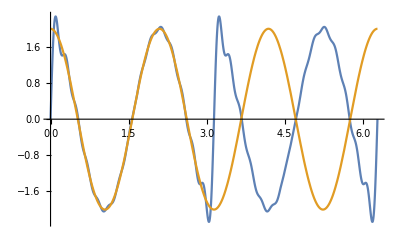

```mathematica
Plot[{Evaluate[myFSin[x,30]],f[x]},{x,0,2L}]
```